```mathematica
f1[x_]:=Cos[x^2]/E^(0.2*x^2)+0.2*x
f2[x_]:=0.2*x
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
lstGrdLin={{-5,-3,3,5},{-1,-0.5,0.5,1}};
lstStyl1={{Blue,Thick},{Green,Thin,Dashed},{Red,Thin}};
lstStyl2={Directive[Thick,14],Directive[Thick,14]};
lstStyl3=Directive[Gray,Dotted];


rLgnd={"f1","f2","f3"};
Plot[{Sin[x^2],x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,3},ImageSize->540,PlotStyle->{{Blue,Thin},{Green,Thick,Dashed},{Red,Thick}},AxesStyle->{Directive[Black,Thick,14],Directive[Blue,Thick,22]},GridLines->{{1,1.5,2,2.5,3},{-6,-3,2,4}},GridLinesStyle->Directive[Gray,Dashed],PlotLabel->Style[Framed["Демонстрационный график с оформлением",FrameStyle->Red,RoundingRadius->5],16,Plain,Blue,Background->LightYellow],PlotLegends->Placed[SwatchLegend[rLgnd,LegendLabel->"Легенда (типы и вид линий):",LegendLayout->"Row",LegendFunction->"Frame"],{{0.2,-0.01},{0.3,-0.8}}]]
```

-Graphics-

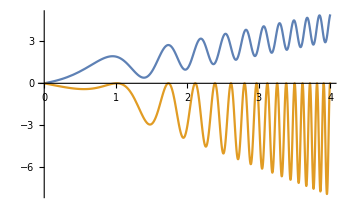
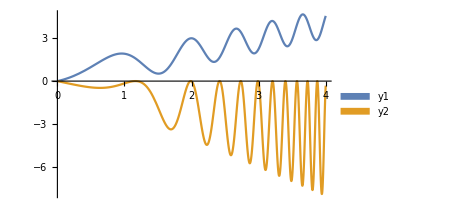

```mathematica
rLgnd={"y1","y2"};
pLgnd="Row";
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,PlotLegends->SwatchLegend[{y1,y2},LegendLayout->"Row"]];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
StringReplace["PlotLegends→SwatchLegend[{"y1","y2"},LegendLayout→"Row"]"," "]
```

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[] , },LegendLayout→ PlotLegends→SwatchLegend[{ Row y1 y2, ].

StringReplace[] , },LegendLayout→ PlotLegends→SwatchLegend[{ Row y1 y2, ]

```mathematica
StringLength[StringReplace[ToString["PlotLegends->SwatchLegend[{y1,y2},LegendLayout->"Row"]"],Whitespace..:>""]]
```

52

```mathematica
Clear[a,b,c,d,z,fRab];
fRab:=c*d+(d*z^4)/(c+d)+d*z^2/(b+z)-(d+z)/(b+c*z^2)+(z*(c+a*z^2))/(d+z^3);
fRab
Numerator[fRab[[4]]]//InputForm
```

c d+(d z^4)/(c+d)+(d z^2)/(b+z)-(d+z)/(b+c z^2)+(z (c+a z^2))/(d+z^3)

-d - z

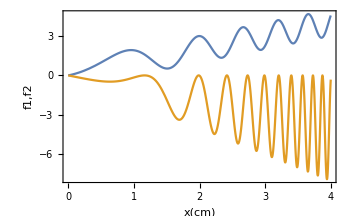
-Graphics--Graphics-

```mathematica
xFrmLbl="x(cm)";
yFrmLbl="f1,f2";
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,Frame->True,FrameLabel->{xFrmLbl,yFrmLbl}];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
lstR={1,4,73,9,-1,41,-7,-73,45,11,-2,40,3,-7,2,-5,11,5,41,8,42,73};
Select[lstR,x_/;Prime[x]&&x>10]
```

{}

```mathematica
bez = StringReplace[ToString["PlotLegends→SwatchLegend[{"y1","y2"},LegendLayout→"Row"]"],Whitespace..:>""]
StringLength[bez]
```

],},LegendLayout→PlotLegends→SwatchLegend[{Rowy1y2

50

```mathematica
"],},LegendLayout→PlotLegends→SwatchLegend[{Rowy1y2"
```